#### Incidence function per group contact rates

```mathematica
B[pops_,dispars_,cv_]:=Module[
{
s=pops[[1]],i=pops[[2]],r=pops[[3]],
β=dispars[[1]],
cs=cv[[1]],ci=cv[[2]],cr=cv[[3]]
},
Return[β cs s (ci i)/(cs s+ci i+cr r)]
]
```

```mathematica
B[{999,1,0},{0.05,1/3},{12,12,12}]
```

0.5994

#### SIR behavior solver function - fixed # of contacts

```mathematica
SIRB[pops_,poppars_,dispars_,cv_,soltimes_]:=

(* 
pops = vector with the S,I,R  initial conditions of the system,
poppars = vector with the popualtion dynamics parameters Λ and μ,
dispars = vector with the disease parameters β and γ,
c = # of contacts made per disease class individuals,
soltimes = times for the partial solution.
*)

Module[{
s0=pops[[1]],i0=pops[[2]],r0=pops[[3]], (*pops*)
Λ=poppars[[1]],μ=poppars[[2]], (*poppars*)
β=dispars[[1]],γ=dispars[[2]], (*dispars*)
cs=cv[[1]],ci=cv[[2]],cr=cv[[3]],(*c*)
int=soltimes[[1]],fint=soltimes[[2]]
},

n=s0+i0+r0;

(* The system *)
ds=s'[t]==Λ-B[{s[t],i[t],r[t]},{β,γ},{cs,ci,cr}]-μ s[t];
di=i'[t]==B[{s[t],i[t],r[t]},{β,γ},{cs,ci,cr}]-(γ+μ) i[t];
dr=r'[t]==γ i[t]-μ r[t];

(* The solution *)
solb=Flatten[
NDSolve[{ds,di,dr,s[int]==s0,i[int]==i0,r[int]==r0},
{s,i,r},{t,int,fint},MaxSteps->10000,PrecisionGoal->20],1];

]
```

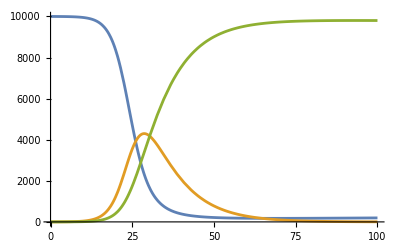

```mathematica
ft=100;
SIRB[{9999,1,0},{1,0.0001},{0.01,1/9},{48,48,48},{0,ft}]
Plot[Evaluate[{s[t],i[t],r[t]}/.solb],{t,0,ft}]
```

#### Maximizer

```mathematica
(*Single peak function*)
fs[x_,y_,z_]:=(x z -z^2)^y

(*The maxer code runs the optimization process*)
Maxer[pops_,dispars_,plan_,disen_]:=Module[{
s=pops[[1]],i=pops[[2]],r=pops[[3]],(* Populations*)
β=dispars[[1]],γ=dispars[[2]], (* Disease parameters *)
T=plan [[1]], (* Time horizon *)

ν=plan[[2]],(* Risk perception *)
cred=disen[[1]], (* Activity reduction of infected ones due to symptoms severity *)
iutred=disen[[2]]  (* Reduced utility obtained while infected *)
},

b=48; (*maximum possible # of contacts, the optimal utility is at half of this*)
maxcr=Floor[b/2];

ci=maxcr (cred);
cr=maxcr;

δ=0.99986; (*discount factor*)

(* Vector storaging the optimal s utility *)
EUS=Table[0,{t,1,T+1}];

(* The individual's goal is to remain suceptible by the end of the planning horizon, so cs=maxcr=12 *)
EUS[[-1]]=fs[b,ν,maxcr];

(* Vector storaging the optimal i utility *)
EUI=Table[0,{t,1,T+1}];

(* Vector storaging the optimal r utility *)
EUR=Table[0,{t,1,T+1}];

(* Vector storaging the optimal contact rate for susceptible individuals *)
cs=Table[0,{i,1,T+1}];

(* The last step is already known, the susceptible indivial wants to be susceptible at the end of the time horizon, then it is assumed that susceptible individuals have an optimized contact rate before the behavior change *)
cs[[-1]]=maxcr;

(* Pii=1-P^z, probability of continuing infectious, independent of the system, it's outside the loop *)
Pii=Exp[-γ];


(* Optimization procedure *)
For[t=T,t≥ 1,t--, (* Horizon times, this goes backwards *)

(* individual's utility starts at zero: will increase*)
maxu=0;

(* Evaluating all the contact rates for susceptible individuals, all possible variable states *)
For[csd=1,csd≤maxcr,csd++, 

(* Probability of continuing susceptible, dependent on the prevalence, that's why it is inside the loop *)
Pss=Exp[-β((csd ci i)/(csd s+ci i+maxcr r))];

(* Evaluating the expected utilities *)

(*Utility gained by being currently susceptible*)
EUS[[t]]= fs[b,ν,csd] +δ(Pss EUS[[t+1]]+(1-Pss) EUI[[t+1]]);

(*Utility gained by being currently Infected*)
EUI[[t]]=iutred fs[b,ν,ci] +δ(Pii EUI[[t+1]]+(1-Pii) EUR[[t+1]]);

(*Utility gained by being currently Recovered*)
EUR[[t]]=fs[b,ν,cr] +δ EUR[[t+1]];

(*Compare the new utility with the previous one, if it's bigger, then adapt the behavior *)
If[EUS[[t]]>maxu,cs[[t]]=csd;maxu=EUS[[t]]]

]
];
Clear[t];
Return[cs]
]
```

#### System solver

```mathematica
(* =-=-=-=-=-= The behavior epidemic model =-=-=-=-=-=-= *)

(*Population parameters*)
Λ=0;μ=Λ/n;

(* Disease parameters *)
β=0.01; γ=1/9.;

(*Optimization parameters*)
T=14;
ν=0.1;
maxcr=24;
cred=1;
iutred=0.;

(* Initial conditions *)
s0=9999;
i0=1;
r0=0;
n=s0+i0+r0;

vars={s[t],i[t],r[t]};

(* Final time *)
 tft=200; 

(*Timestep lengths*)
Δt=1;

(* Intervention times *)
times=Table[i,{i,0,tft,Δt}];
dim=Length[times];

(* Infected and recovered contacts rates (fixed) *)
ci=Floor[maxcr(cred)];cr=maxcr;

(*Predefine lists*)
ctime=Table[0,{k,0,tft}];

ctime[[1]]=maxcr;

(* Solutions loop *)

popstime={};

For[k=1,k<dim,k++,

AppendTo[popstime,{s0,i0,r0}];

(*=-=-=-=-=-=-=-=-=-=-=-= Disease dynamics =-=-=-=-=-=-=-=-=-=-=-=*)

(* SIR solver under current system state *) 
SIRB[{s0,i0,r0},{Λ,μ},{β,γ},{ctime[[k]],ci,cr},{times[[k]],times[[k+1]]}];

(* Updating population's distribution *)
{s0,i0,r0}=Flatten[Table[#/.solb,{t,times[[k+1]],times[[k+1]]}]&/@vars];

(* Updating susceptible individual's contacts *)
cst=Maxer[{s0,i0,r0},{β,γ},{T,ν},{cred,iutred}][[1]];

ctime[[k+1]]=cst

]
```

#### Disease dynamics

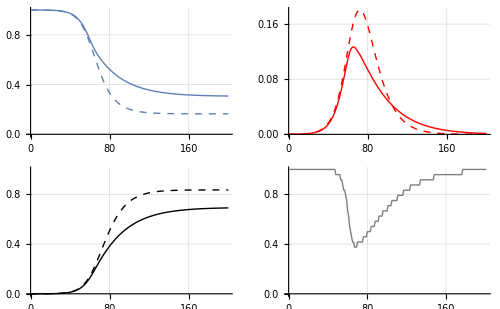

```mathematica
SIRB[{9999,1,0},{0,0},{β,γ},{maxcr,ci,maxcr},{0,tft}]

pnobs=Plot[Evaluate[(s[t]/.solb)/n],{t,0,tft},PlotRange->{0,1},PlotStyle->{Thick,Dashed},TicksStyle->Directive[Bold, 12],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed]];

pnobi=Plot[Evaluate[(i[t]/.solb)/n],{t,0,tft},PlotRange->All,PlotStyle->{Thick,Dashed,Red},TicksStyle->Directive[Bold, 12],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed]];

pnobr=Plot[Evaluate[(r[t]/.solb)/n],{t,0,tft},PlotRange->{0,1},PlotStyle->{Thick,Dashed,Black},TicksStyle->Directive[Bold, 12],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed]];

sbe=ListLinePlot[popstime[[;;,1]]/n,PlotRange->{0,1},PlotStyle->{Thick}];
ibe=ListLinePlot[popstime[[;;,2]]/n,PlotRange->{0,1},PlotStyle->{Thick,Red}];
rbe=ListLinePlot[popstime[[;;,3]]/n,PlotRange->{0,1},PlotStyle->{Thick,Black}];

csplot=ListLinePlot[ctime/maxcr,PlotStyle->{Thick,GrayLevel[0.5]},TicksStyle->Directive[Bold, 12],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],PlotRange->{0,1}];

GraphicsGrid[{{Show[pnobs,sbe],Show[pnobi,ibe]},{Show[pnobr,rbe],Show[csplot]}},ImageSize->500]
```